## Model

### Variables

```mathematica
(*B0 to be determined with regression.*)
R = 1;
z0 = 2;
g = 10;
Clear[B0]
```

### Model

```mathematica
AccelMotion[t_] := z0 - g t^2/2;
Field[z_] := B0 R^3/(R^2+z^2)^(3/2);


AccelField[t_] := Composition[Field, AccelMotion][t];
AccelFlux[t_] := -Pi R^3 AccelField'[t];
```

### Minima

```mathematica
(*Finding minimum after time t = 0 of AccelFlux.*)
minimumVoltageModel = t/.Solve[AccelFlux'[t] == 0, t, Reals][[2]];
(*Shifting AccelFlux minimum to t = 0.*)
AccelFluxShifted[t_] := AccelFlux[t + minimum];
```

## Data

```mathematica
filePath = "E:\\Users\\USER\\Documents\\UNAM\\Cuarto Semestre\\Lab\\Tercer reporte";
fileName = "test.txt";
fullName = StringJoin[{filePath, "\\", fileName}];
data = Import[fullName, "Data"];
(*We'll shift the date so as to have the first minimum at t = 0.*)
positionOfMinimum = Position[data[[All, 2]], Min[data[[All, 2]]]][[1, 1]];
timeOfMinimum = data[[positionOfMinimum, 1]];

data = MapAt[# - timeOfMinimum &, data, {All, 1}];
```

## Fitting

FittedModel[…]

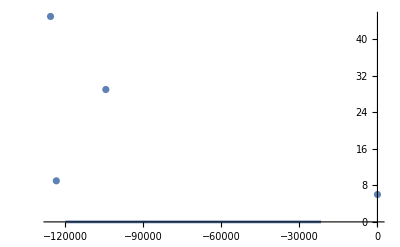

```mathematica
fitModel = NonlinearModelFit[data, AccelFluxShifted[t], B0, t]
Show[ListPlot[data],Plot[fitModel[t], {t, -120000, 10}]]
```